Define the values for the boundary points

```mathematica
Clear[u]
```

```mathematica
boundary={{1,0},{3,0},{0,1},{2,3},{3,3},{2,0},{4,1},{4,2},{1,2}};
```

```mathematica
(u[#]=0)&/@boundary[[1;;5]];
(u[#]=1)&/@boundary[[6;;]];
```

Define the values for the interior points

```mathematica
interior={{1,1},{2,1},{2,2},{3,1},{3,2}};
(u[#]=0.5)&/@interior;
```

Update using Monte Carlo

```mathematica
Do[{i,j}=RandomChoice[interior];
u[{i,j}]=1/4*(u[{i-1,j}]+u[{i+1,j}]+u[{i,j+1}]+u[{i,j-1}]),{1000}]
```

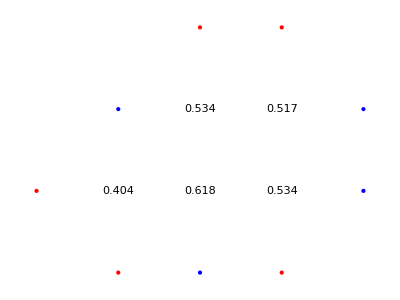

```mathematica
interiorVals=u/@interior;
Graphics[{PointSize[Large],{Red,Point/@boundary[[1;;5]]},{Blue,Point/@boundary[[6;;]]},Text[#[[1]]~NumberForm~3,#[[2]]]&/@({interiorVals,interior}//Transpose)}]
```

Solve using matrices

```mathematica
LinearSolve[{{1,-1/4,0,-1/4,0},{-1/4,1,0,0,-1/4},{0,0,1,-1/4,0},{-1/4,0,-1/4,1,-1/4},{0,-1/4,0,-1/4,1}},{1/4,1/4,1/4,1/4,1/4}]
```

{95/178,46/89,36/89,55/89,95/178}

### sandbox

```mathematica
xyvals=Union[boundary,interior];
zvals=u/@xyvals;
data=Append[xyvals//Transpose,zvals]//Transpose;
ListPlot3D[data,AxesLabel->{"X","Y","Z"}]
```